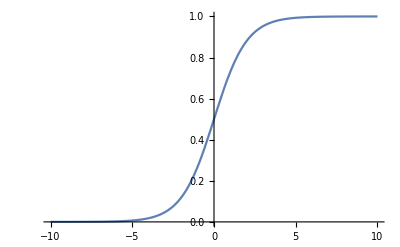

```mathematica
ss0[x_] := 1/(1+Exp[-x]);
Plot[ss0[x],{x,-10,10}]
```

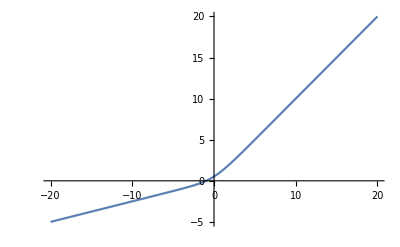

```mathematica
ss1[x_] := Log[1+Exp[x]]
Plot[ss1[x],{x,-20,20}]
```

## 3 neuron network

One input neuron + one output neuron;  a single neuron in a single hidden layer.
4 parameters:  w11 from input to hidden, b1 for hidden, w21 from hidden to output, b2 for output

```mathematica
nnfunc3[x_, w11_,w21_,b1_,b2_] :=  ss0[w21*ss0[w11*x+b1] +b2]    (* The effect of the network is this function *)
```

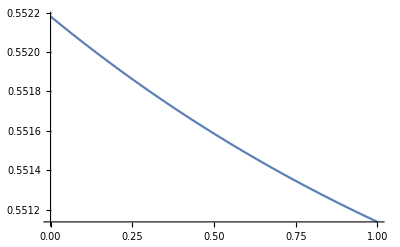

```mathematica
Plot[nnfunc3[x,0.61,-0.2,3,0.4],{x,0,1}]
```

```mathematica
targetfunc[x_] := x^2;   Plot[targetfunc[x],{x,-1.1,1.1}];  
(* The function we want to use the neural network for *)
xmin = -1;xmax = 1;  xwidth = (xmax-xmin);    (*  Set range of x *)
```

```mathematica
nT=100.0 ; (* Integral discretized into nT intervals; nT+1 test/training values *)
xvec = Table[x,{x,xmin,xmax,xwidth/nT}]     
(* This is either/both the training set or the test set.   *)
LL0[w11_,w21_,b1_,b2_] := (xwidth/nT)*Sum[(nnfunc3[xvec[[ii]],w11,w21,b1,b2]-targetfunc[xvec[[ii]]])^2,{ii,1,Length[xvec]}]
(* The loss function.  This is what we will minimize.  *)
```

{-1.,-0.98,-0.96,-0.94,-0.92,-0.9,-0.88,-0.86,-0.84,-0.82,-0.8,-0.78,-0.76,-0.74,-0.72,-0.7,-0.68,-0.66,-0.64,-0.62,-0.6,-0.58,-0.56,-0.54,-0.52,-0.5,-0.48,-0.46,-0.44,-0.42,-0.4,-0.38,-0.36,-0.34,-0.32,-0.3,-0.28,-0.26,-0.24,-0.22,-0.2,-0.18,-0.16,-0.14,-0.12,-0.1,-0.08,-0.06,-0.04,-0.02,0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.}

```mathematica
(*  Minimization attempts *)
sol0 = FindMinimum[LL0[w11, w21,b1,b2], {{w11,-9}, {w21,31},{b1,-1.3},b2}, MaxIterations->10000, Method->"ConjugateGradient"]
```

{0.420267,{w11→-43.3992,w21→26.2193,b1→-142.843,b2→-298.654}}

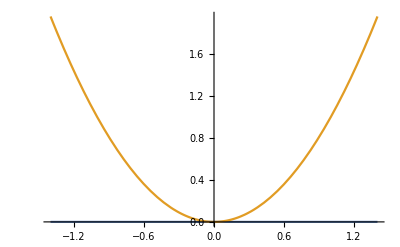

```mathematica
Plot[{(nnfunc3[x,w11,w21,b1,b2] /. sol0[[2]]), targetfunc[x]},{x,xmin-0.2*xwidth,xmax+0.2*xwidth}]
```

```mathematica
l01 = Table[{x, (nnfunc3[x,w11,w21,b1,b2] /. sol0[[2]]), targetfunc[x]}, {x,xmin,xmax, xwidth/(2.0*nT)}];
Export["tttest.dat",l01];
strm=OpenAppend["tttest.dat"];WriteString[strm,"\n"];Close[strm]
```

tttest.dat

```mathematica
sol0 = FindMinimum[LL0[w11, w21,b1,b2], {{w11,5}, {w21,-10.1},b1,b2}, MaxIterations->1000]
```

{0.119308,{w11→10.4274,w21→-3.95432,b1→8.58523,b2→2.8891}}

```mathematica
sol0 = FindMinimum[LL0[w11, w21,b1,b2], {{w11,RandomReal[{-10,20}]}, {w21,RandomReal[{200,-100}]},{b1,RandomReal[{-32,32}]},{b2,RandomReal[{-20,20}]}}, MaxIterations->1000]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{0.171486,{w11→0.144462,w21→26.7577,b1→11.6897,b2→-316.032}}

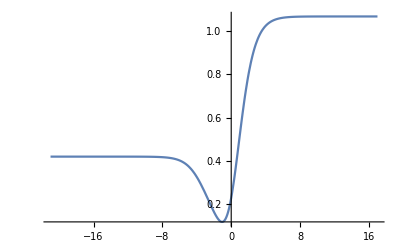

```mathematica
Plot[LL0[ -10.43, 3.954, -8.6, b2], {b2,-31,17}, PlotRange->All]
```

```mathematica
l01 = Table[{vv, LL0[ vv, 3.954,  -8.585, -1.065]}, {vv,-80,80,0.2}];
Export["tttest.dat",l01];
strm=OpenAppend["tttest.dat"];WriteString[strm,"\n"];Close[strm]
```

tttest.dat

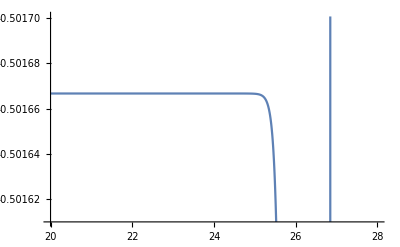

```mathematica
Plot[LL0[0.14446, w21,11.69, -316], {w21,20,28}]
```

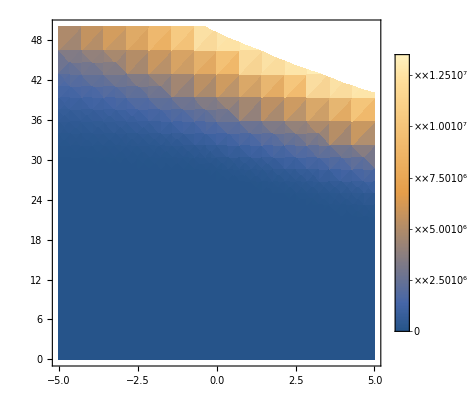

```mathematica
DensityPlot[LL0[w11, w21,11.69,-316.03], {w11,-5,5},{w21,0,50}, PlotLegends->Automatic]
```

```mathematica
Plot3D[LL0[w11, w21,3.8, 167], {w11,-5,5},{w21,-210,100}]
```

-Graphics3D-

```mathematica
FindMinimum[LL0[w11, w21,b1,b2], {w11, w21,b1,b2}]
```

FindMinimum::srect: Value w21 in search specification {w11,w21,b1,b2} is not a number or array of numbers.

FindMinimum[LL0[w11,w21,b1,b2],{w11,w21,b1,b2}]

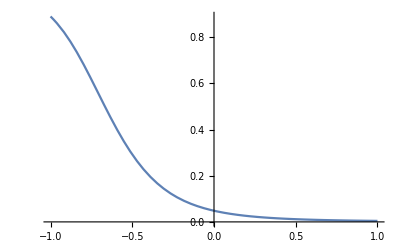

```mathematica
Plot[nnfunc0[x,-0.802, 106.44,-3.113, -7.513],{x,-1,1}]
```

```mathematica
nnfuncT[x_, w11_,w12_, w21_,w22_,b1_,b2_,b3_] :=  ss0[w21*ss0[w11*x+b1] + w22*ss0[w12*x+b2]+b3]
```

```mathematica
nnfuncT[0.2,0.61,2,0.13,0.4, -1, 1.4]
```

0.821663

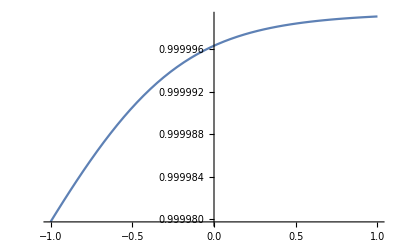

```mathematica
Plot[nnfuncT[x,0.61,2,3,0.4,0.3,9],{x,-1,1}]
```

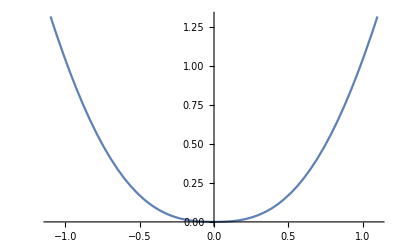

```mathematica
targetfunc[x_] := x^2*(0.2+Abs[Sin[x]]);  Plot[targetfunc[x],{x,-1.1,1.1}]
```

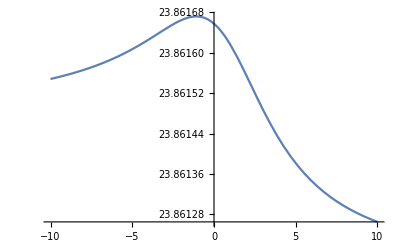

```mathematica
xvec = Table[x,{x,-1,1,0.05}];
LLT[w11_,w12_,w21_,w22_,b1_,b2_,b3_] := Sum[(nnfuncT[xvec[[ii]],w11,w12,w21,w22,b1,b2,b3]-targetfunc[xvec[[ii]]])^2,{ii,1,Length[xvec]}]
Plot[LLT[w11, 1,2,3,0.4,0.3,9], {w11,-10,10}]
```

```mathematica
sol0=FindMinimum[LLT[w11,w12,w21,w22,b1,b2,b3],{w11,w12,w21,w22,b1,b2,b3},MaxIterations->100000]
```

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{4.96468,{w11→-107.066,w12→-107.066,w21→86.3934,w22→86.3934,b1→-74.3314,b2→-74.3314,b3→-112.499}}

```mathematica
sol0=FindMinimum[LLT[w11,w12,w21,w22,b1,b2,b3],{{w11,10},{w12,-30},{w21,0.5},{w22,0.4},{b1,2},{b2,-1},{b3,0.3}},MaxIterations->10000]
```

{10.7244,{w11→-16.3212,w12→-726.059,w21→-34.5899,w22→-58.396,b1→64.4284,b2→2.11749,b3→-5.04982}}

```mathematica
sol0=FindMinimum[LLT[w11,w12,w21,w22,b1,b2,b3],{{w11,-41},{w12,30},{w21,0.5},{w22,0.4},{b1,2},{b2,-1},{b3,0.3}},MaxIterations->10000, Method->"ConjugateGradient"]
```

{4.91161,{w11→-41.0095,w12→29.993,w21→-10.6881,w22→-9.31994,b1→1.80512,b2→-1.21221,b3→-20.3613}}

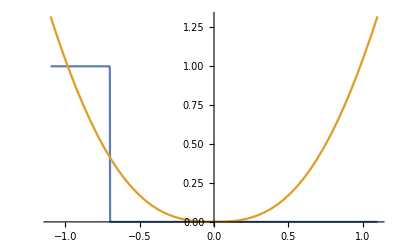

```mathematica
Plot[{(nnfuncT[x,w11,w12,w21,w22,b1,b2,b3] /. sol0[[2]]), targetfunc[x]},{x,-1.1,1.1}]
```